```mathematica
RiemannPrimeCounting[n_]:=Sum[PrimePi[n^(1/j)]/j,{j,1,N[Log[n]/Log[2]]}]
d[n_,z_]:=Product[1/(p[[2]]!) Pochhammer[z,p[[2]]],{p,FI[n]}];FI[n_]:=If[n==1,{},FactorInteger[n]]
DD[n_,k_]:=Sum[d[j,k],{j,1,n}]
LinniksIdentityExpanded[n_,a_]:=Sum[(-1)^(k+1)/k Sum[(-1)^(k-j) Binomial[k,j] DD[n,a j],{j,0,k}],{k,1,N[Log[n]/Log[2]]}]
Table[{n,N[RiemannPrimeCounting[n]],N[LinniksIdentityExpanded[n,1/10]]*10},{n,1,100}]//TableForm
```

1 | 0. | 0.
2 | 1. | 1.
3 | 2. | 2.
4 | 2.5 | 2.5
5 | 3.5 | 3.5
6 | 3.5 | 3.5
7 | 4.5 | 4.5
8 | 4.83333 | 4.83333
9 | 5.33333 | 5.33333
10 | 5.33333 | 5.33333
11 | 6.33333 | 6.33333
12 | 6.33333 | 6.33333
13 | 7.33333 | 7.33333
14 | 7.33333 | 7.33333
15 | 7.33333 | 7.33333
16 | 7.58333 | 7.58333
17 | 8.58333 | 8.58333
18 | 8.58333 | 8.58333
19 | 9.58333 | 9.58333
20 | 9.58333 | 9.58333
21 | 9.58333 | 9.58333
22 | 9.58333 | 9.58333
23 | 10.5833 | 10.5833
24 | 10.5833 | 10.5833
25 | 11.0833 | 11.0833
26 | 11.0833 | 11.0833
27 | 11.4167 | 11.4167
28 | 11.4167 | 11.4167
29 | 12.4167 | 12.4167
30 | 12.4167 | 12.4167
31 | 13.4167 | 13.4167
32 | 13.6167 | 13.6167
33 | 13.6167 | 13.6167
34 | 13.6167 | 13.6167
35 | 13.6167 | 13.6167
36 | 13.6167 | 13.6167
37 | 14.6167 | 14.6167
38 | 14.6167 | 14.6167
39 | 14.6167 | 14.6167
40 | 14.6167 | 14.6167
41 | 15.6167 | 15.6167
42 | 15.6167 | 15.6167
43 | 16.6167 | 16.6167
44 | 16.6167 | 16.6167
45 | 16.6167 | 16.6167
46 | 16.6167 | 16.6167
47 | 17.6167 | 17.6167
48 | 17.6167 | 17.6167
49 | 18.1167 | 18.1167
50 | 18.1167 | 18.1167
51 | 18.1167 | 18.1167
52 | 18.1167 | 18.1167
53 | 19.1167 | 19.1167
54 | 19.1167 | 19.1167
55 | 19.1167 | 19.1167
56 | 19.1167 | 19.1167
57 | 19.1167 | 19.1167
58 | 19.1167 | 19.1167
59 | 20.1167 | 20.1167
60 | 20.1167 | 20.1167
61 | 21.1167 | 21.1167
62 | 21.1167 | 21.1167
63 | 21.1167 | 21.1167
64 | 21.2833 | 21.2833
65 | 21.2833 | 21.2833
66 | 21.2833 | 21.2833
67 | 22.2833 | 22.2833
68 | 22.2833 | 22.2833
69 | 22.2833 | 22.2833
70 | 22.2833 | 22.2833
71 | 23.2833 | 23.2833
72 | 23.2833 | 23.2833
73 | 24.2833 | 24.2833
74 | 24.2833 | 24.2833
75 | 24.2833 | 24.2833
76 | 24.2833 | 24.2833
77 | 24.2833 | 24.2833
78 | 24.2833 | 24.2833
79 | 25.2833 | 25.2833
80 | 25.2833 | 25.2833
81 | 25.5333 | 25.5333
82 | 25.5333 | 25.5333
83 | 26.5333 | 26.5333
84 | 26.5333 | 26.5333
85 | 26.5333 | 26.5333
86 | 26.5333 | 26.5333
87 | 26.5333 | 26.5333
88 | 26.5333 | 26.5333
89 | 27.5333 | 27.5333
90 | 27.5333 | 27.5333
91 | 27.5333 | 27.5333
92 | 27.5333 | 27.5333
93 | 27.5333 | 27.5333
94 | 27.5333 | 27.5333
95 | 27.5333 | 27.5333
96 | 27.5333 | 27.5333
97 | 28.5333 | 28.5333
98 | 28.5333 | 28.5333
99 | 28.5333 | 28.5333
100 | 28.5333 | 28.5333

```mathematica
Li[n_,a_,k_]:= Sum[(-1)^(k-j) Binomial[k,j] DD[n,a j],{j,0,k}]
```

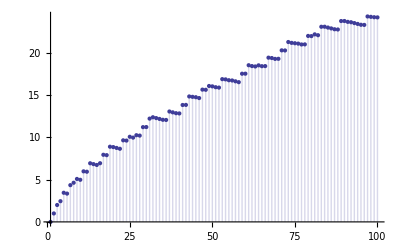

```mathematica
DiscretePlot[Li[n,-(1/10),1]/(-1/10),{n,1,100}]
```

```mathematica
Series[ ((x+1)^b-1)/b,{x,0,30}]
```

x+1/2 (-1+b) x^2+1/6 (-2+b) (-1+b) x^3+1/24 (-3+b) (-2+b) (-1+b) x^4+1/120 (-4+b) (-3+b) (-2+b) (-1+b) x^5+1/720 (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^6+((-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^7)/5040+((-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^8)/40320+((-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^9)/362880+((-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^10)/3628800+((-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^11)/39916800+1/479001600(-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^12+1/6227020800(-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^13+1/87178291200(-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^14+1/1307674368000(-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^15+1/20922789888000(-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^16+1/355687428096000(-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^17+1/6402373705728000(-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^18+1/121645100408832000(-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^19+1/2432902008176640000(-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^20+((-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^21)/51090942171709440000+((-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^22)/1124000727777607680000+((-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^23)/25852016738884976640000+((-23+b) (-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^24)/620448401733239439360000+((-24+b) (-23+b) (-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^25)/15511210043330985984000000+((-25+b) (-24+b) (-23+b) (-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^26)/403291461126605635584000000+((-26+b) (-25+b) (-24+b) (-23+b) (-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^27)/10888869450418352160768000000+((-27+b) (-26+b) (-25+b) (-24+b) (-23+b) (-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^28)/304888344611713860501504000000+((-28+b) (-27+b) (-26+b) (-25+b) (-24+b) (-23+b) (-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^29)/8841761993739701954543616000000+((-29+b) (-28+b) (-27+b) (-26+b) (-25+b) (-24+b) (-23+b) (-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^30)/265252859812191058636308480000000+O[x]^31

```mathematica
FF[x_, b_] := x+1/2 (-1+b) x^2+1/6 (-2+b) (-1+b) x^3+1/24 (-3+b) (-2+b) (-1+b) x^4+1/120 (-4+b) (-3+b) (-2+b) (-1+b) x^5+1/720 (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^6+((-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^7)/5040+((-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^8)/40320+((-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^9)/362880+((-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^10)/3628800+((-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^11)/39916800+1/479001600(-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^12+1/6227020800(-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^13+1/87178291200(-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^14+1/1307674368000(-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^15+1/20922789888000(-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^16+1/355687428096000(-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^17+1/6402373705728000(-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^18+1/121645100408832000(-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^19+1/2432902008176640000(-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^20+((-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^21)/51090942171709440000+((-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^22)/1124000727777607680000+((-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^23)/25852016738884976640000+((-23+b) (-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^24)/620448401733239439360000+((-24+b) (-23+b) (-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^25)/15511210043330985984000000+((-25+b) (-24+b) (-23+b) (-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^26)/403291461126605635584000000+((-26+b) (-25+b) (-24+b) (-23+b) (-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^27)/10888869450418352160768000000+((-27+b) (-26+b) (-25+b) (-24+b) (-23+b) (-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^28)/304888344611713860501504000000+((-28+b) (-27+b) (-26+b) (-25+b) (-24+b) (-23+b) (-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^29)/8841761993739701954543616000000+((-29+b) (-28+b) (-27+b) (-26+b) (-25+b) (-24+b) (-23+b) (-22+b) (-21+b) (-20+b) (-19+b) (-18+b) (-17+b) (-16+b) (-15+b) (-14+b) (-13+b) (-12+b) (-11+b) (-10+b) (-9+b) (-8+b) (-7+b) (-6+b) (-5+b) (-4+b) (-3+b) (-2+b) (-1+b) x^30)/265252859812191058636308480000000
```

n-n^2+n^3-n^4+n^5-n^6+n^7-n^8+n^9-n^10+n^11-n^12+n^13-n^14+n^15-n^16+n^17-n^18+n^19-n^20+n^21-n^22+n^23-n^24+n^25-n^26+n^27-n^28+n^29-n^30

```mathematica
FF[x,-1]
Series[(-1/(x+1))+1,{x,0,30}]
```

x-x^2+x^3-x^4+x^5-x^6+x^7-x^8+x^9-x^10+x^11-x^12+x^13-x^14+x^15-x^16+x^17-x^18+x^19-x^20+x^21-x^22+x^23-x^24+x^25-x^26+x^27-x^28+x^29-x^30

x-x^2+x^3-x^4+x^5-x^6+x^7-x^8+x^9-x^10+x^11-x^12+x^13-x^14+x^15-x^16+x^17-x^18+x^19-x^20+x^21-x^22+x^23-x^24+x^25-x^26+x^27-x^28+x^29-x^30+O[x]^31

```mathematica
FF[x,0]
Series[Log[x+1],{x,0,30}]
```

x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+x^9/9-x^10/10+x^11/11-x^12/12+x^13/13-x^14/14+x^15/15-x^16/16+x^17/17-x^18/18+x^19/19-x^20/20+x^21/21-x^22/22+x^23/23-x^24/24+x^25/25-x^26/26+x^27/27-x^28/28+x^29/29-x^30/30

x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+x^9/9-x^10/10+x^11/11-x^12/12+x^13/13-x^14/14+x^15/15-x^16/16+x^17/17-x^18/18+x^19/19-x^20/20+x^21/21-x^22/22+x^23/23-x^24/24+x^25/25-x^26/26+x^27/27-x^28/28+x^29/29-x^30/30+O[x]^31

```mathematica
Log[1+.9]
```

0.641854

```mathematica
FF[.9,-1]
```

0.453604

```mathematica
1/(.9+1)
```

0.526316

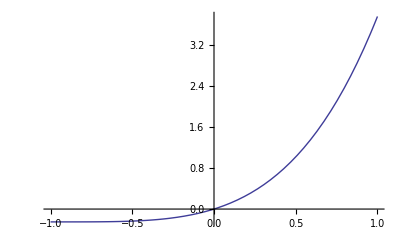

```mathematica
Plot[ FF[n,4],{n,-1,1}]
```

```mathematica
Animate[Plot[ FF[n,Cos[k].5+.5],{n,-1,1}],{k,0,2 Pi,.0001}]
```

```mathematica
K[n_]:=FullSimplify[MangoldtLambda[n]/Log[n]]
P[n_,k_]:=P[n,k]=Sum[K[j] P[Floor[n/j],k-1],{j,2,n}];P[n_,0]:=1
DD[n_,k_]:=Sum[k^j/j! P[n,j],{j,0,Log[2,n]}]
Animate[DiscretePlot[(DD[n,z=Cos[k].5+.5]-1)/z,{n,1,100}],{k,0,2 Pi,.0001}]
```

```mathematica
PlotRange->{{1,100},{-10,10}}
```

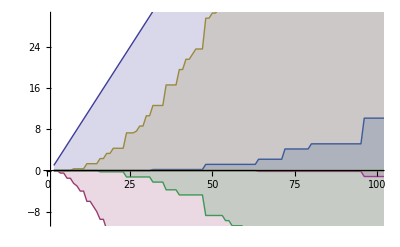

```mathematica
d[n_,z_]:=d[n,z]=Product[1/(p[[2]]!) Pochhammer[z,p[[2]]],{p,FI[n]}];FI[n_]:=If[n==1,{},FactorInteger[n]]
DD[n_,k_]:=DD[n,k]=Sum[d[j,k],{j,1,n}]
Li[n_,a_,k_]:= Li[n,a,k]=(-1)^(k+1)/k Sum[(-1)^(k-j) Binomial[k,j] DD[n,a j],{j,0,k}]
DiscretePlot[{ Li[n,ss=1,1]/ss, Li[n,ss,2]/ss, Li[n,ss,3]/ss, Li[n,ss,4]/ss, Li[n,ss,5]/ss, Li[n,ss,6]/ss, Li[n,ss,7]/ss, Li[n,ss,8]/ss},{n,2,1000},PlotRange->{{1,100},{-10,30}}]
```